```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\mouze\Desktop\CM_labs\lab10\lab10\lab10

```mathematica
matrix = Import["test_k.txt","Table"];
matrix2 = Import["test_c.txt","Table"];
```

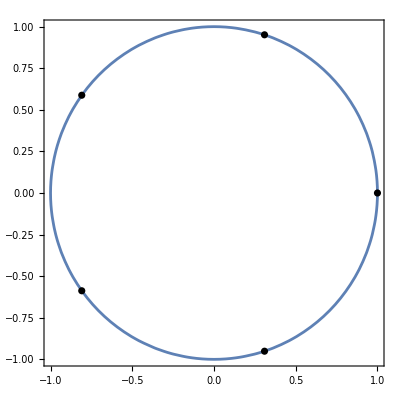

```mathematica
Show[ContourPlot[x^2+y^2==1,{x,-1,1},{y,-1,1}],ListPlot[{ matrix2},AspectRatio->1,PlotStyle->Black],PlotRange->All]
```

```mathematica
R = Import["R.txt","List"]
```

{}

```mathematica
graf = ListPlot[R,PlotRange->All,ImageSize->600, AxesLabel->{"Количество точек", "R"}]
```

-Graphics-

```mathematica
(*Export["R.jpg", graf]*)
```